```mathematica
1+1
```

2

```mathematica
elcdm[z_]=√(om (1+z)^3+1-om)
```

√(1-om+om (1+z)^3)

```mathematica
elinear[z_] = Sqrt[om(1+z)^3 + (1- om)(1+z)^(3(1+w0linear - w1linear)) Exp[3 w1linear z]]
```

√(om (1+z)^3+ⅇ^(3 w1linear z) (1-om) (1+z)^(3 (1+w0linear-w1linear)))

```mathematica
elinder[z_] = Sqrt[om(1+z)^3 + (1-om)(1+z)^(3(1 + w0linder + w1linder))Exp[3 w1linder (1/(1+z) - 1)]]
```

√(om (1+z)^3+ⅇ^(3 w1linder (-1+1/(1+z))) (1-om) (1+z)^(3 (1+w0linder+w1linder)))

```mathematica
eode[z_] = Sqrt[om (1+z)^3 + a1 Cos[a2 z^2 + a3] + (1 - a1 Cos[a3] - om)]
```

√(1-om+om (1+z)^3-a1 Cos[a3]+a1 Cos[a3+a2 z^2])

```mathematica
q[z_, e_]= -1 + (1+z)e'[z]/e[z]
```

-1+((1+z) e'[z])/e[z]

```mathematica
r[z_, e_]= q[z,e] (2 q[z,e] + 1) + (1+z)D[q[z,e],z]//Simplify
```

1+((1+z)^2 e'[z]^2)/e[z]^2+((1+z) (-2 e'[z]+(1+z) e''[z]))/e[z]

```mathematica
qLCDM= q[z, elcdm]
```

-1+(3 om (1+z)^3)/(2 (1-om+om (1+z)^3))

```mathematica
rLCDM=r[z,elcdm]//Simplify
```

1

```mathematica
qLinear = q[z, elinear]//Simplify
```

(-om (1+z)^(3 w1linear)+ⅇ^(3 w1linear z) (-1+om) (1+z)^(3 w0linear) (1+3 w0linear+3 w1linear z))/(2 ⅇ^(3 w1linear z) (-1+om) (1+z)^(3 w0linear)-2 om (1+z)^(3 w1linear))

```mathematica
rLinear=r[z,elinear]//Simplify
```

(-2 om (1+z)^(3 w1linear)+ⅇ^(3 w1linear z) (-1+om) (1+z)^(3 w0linear) (2+9 w0linear^2+9 w1linear^2 z^2+3 w1linear (1+4 z)+9 w0linear (1+2 w1linear z)))/(2 ⅇ^(3 w1linear z) (-1+om) (1+z)^(3 w0linear)-2 om (1+z)^(3 w1linear))

```mathematica
qLinder = q[z, elinder]//Simplify
```

-1+(-3 ⅇ^((3 w1linder z)/(1+z)) om (1+z)+3 (-1+om) (1+z)^(3 (w0linder+w1linder)) (1+w0linder+z+w0linder z+w1linder z))/(2 (1+z) (-ⅇ^((3 w1linder z)/(1+z)) om+(-1+om) (1+z)^(3 (w0linder+w1linder))))

```mathematica
rLinder=r[z,elinder]//Simplify
```

(-2 om (1+z)^2+ⅇ^(-(3 w1linder z)/(1+z)) (-1+om) (1+z)^(3 (w0linder+w1linder)) (9 w1linder^2 z^2+2 (1+z)^2+9 w0linder^2 (1+z)^2+9 w0linder (1+z) (1+z+2 w1linder z)+3 w1linder (1+4 z+3 z^2)))/(2 (1+z)^2 (-om+ⅇ^(-(3 w1linder z)/(1+z)) (-1+om) (1+z)^(3 (w0linder+w1linder))))

```mathematica
qOA = q[z, eode]//Simplify
```

-1+((1+z) (3 om (1+z)^2-2 a1 a2 z Sin[a3+a2 z^2]))/(2 (1-om+om (1+z)^3-a1 Cos[a3]+a1 Cos[a3+a2 z^2]))

```mathematica
rOA=r[z,eode]//Simplify
```

(1+3 om z+3 om z^2+om z^3-a1 Cos[a3]-a1 (-1+2 a2^2 z^2 (1+z)^2) Cos[a3+a2 z^2]-a1 a2 Sin[a3+a2 z^2]+a1 a2 z^2 Sin[a3+a2 z^2])/(1+3 om z+3 om z^2+om z^3-a1 Cos[a3]+a1 Cos[a3+a2 z^2])

```mathematica
om = 0.3;
w0linear = -1.25;
w1linear = 1.97;
w0linder=-1.29;
w1linder= 2.84;
a1 = -3.36;
a2= 2.12;
a3 = -0.06 Pi;
```

```mathematica
ploteLCDM = Plot[elcdm[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"LCDM"];
```

```mathematica
ploteLinear = Plot[elinear[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"Linear"];
```

```mathematica
ploteLinder = Plot[elinder[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"Linder"];
```

```mathematica
ploteOA = Plot[eode[z], {z, 0, 3}, AxesLabel->{"z", "E"}, PlotLabel->"OA"];
```

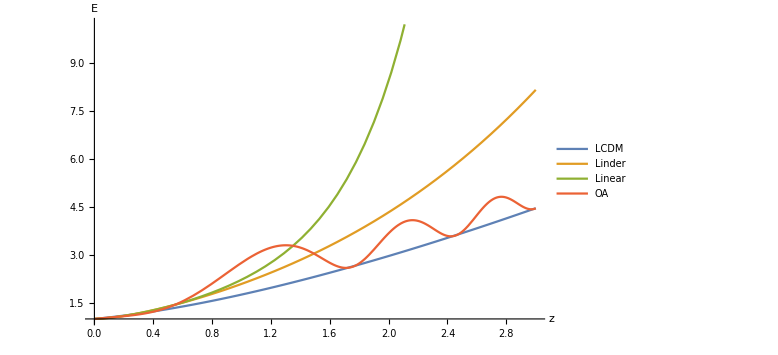

```mathematica
plotE=Plot[{elcdm[z], elinder[z], elinear[z], eode[z]}, {z, 0, 3}, PlotLegends->{"LCDM", "Linder", "Linear", "OA"}, AxesLabel->{Style["z", Black, FontSize->20], Style["E", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

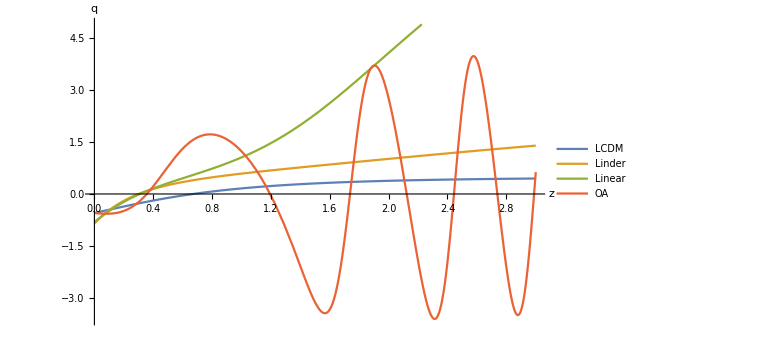

```mathematica
plotq=Plot[{q[z, elcdm], q[z,elinder], q[z,elinear], q[z,eode]}, {z, 0, 3}, PlotLegends->{"LCDM", "Linder", "Linear", "OA"}, AxesLabel->{Style["z", Black, FontSize->20], Style["q", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```

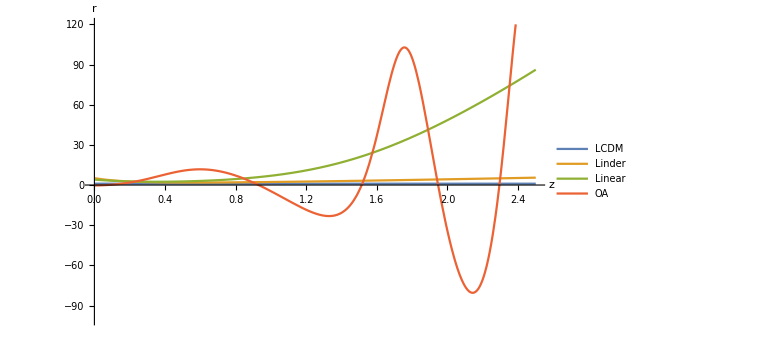

```mathematica
plotr=Plot[{r[z, elcdm], r[z,elinder], r[z,elinear], r[z,eode]}, {z, 0, 2.5}, PlotRange->{-100,120},PlotLegends->{"LCDM", "Linder", "Linear", "OA"}, AxesLabel->{Style["z", Black, FontSize->20], Style["r", Black, FontSize->20]}, PlotStyle->Thick, ImageSize->Large]
```